```mathematica
Clear["Global`*"]
```

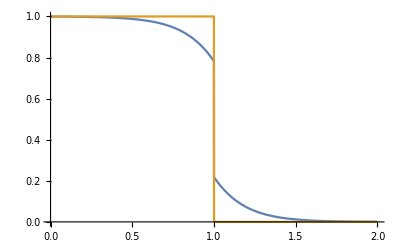

```mathematica
(*n[k_]:=HeavisideTheta[1-k]*)
n[x_]:=Piecewise[{{Tanh[-3(x-0.35-1)],0≤x≤ 1},{Tanh[-3(x+0.35-1)]+1,x>1}}]
n0[x_]:=HeavisideTheta[1-k];
Plot[{n[k],n0[k]},{k,0,2},Exclusions->None]
```

```mathematica
J[Q_]:=NIntegrate[n[k]k,{k,Q,10}];
J0[Q_]:=1/2(1-Q^2)HeavisideTheta[1-Q];
```

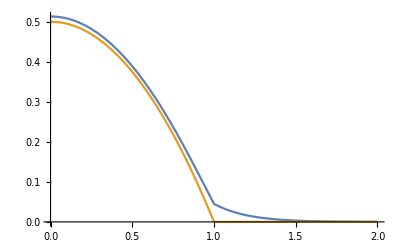

```mathematica
Plot[{J[Q],J0[Q]},{Q,0,2}]
```